# PH401 HW1

## 20220160 Jungeun Kim

```mathematica
Z:=1
Subscript[a, 0]:= 1
```

## Prob 1 (h)

```mathematica
Subscript[R, 1, 0] [r_] := 2 (Z/Subscript[a, 0])^(3/2)Exp[-(Z*r)/Subscript[a, 0]]
```

```mathematica
Subscript[R, 2, 0][r_] := 2 (Z/(2 Subscript[a, 0]))^(3/2)(1-Z/(2 Subscript[a, 0])r)Exp[-(Z*r)/(2 Subscript[a, 0])]
```

```mathematica
Subscript[R, 2, 1][r_] := 1/(√3) (Z/(2 Subscript[a, 0]))^(3/2)Z/Subscript[a, 0] r Exp[-(Z*r)/(2 Subscript[a, 0])]
```

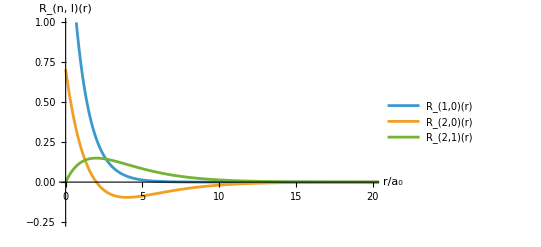

```mathematica
Plot[{Subscript[R, 1, 0] [r] , Subscript[R, 2, 0] [r], Subscript[R, 2, 1] [r]  }, {r, 0, 100}, PlotRange->{{0,20},{-0.25, 1}},
AxesLabel->{Style["r/a_0", Bold, 16],Style["R_(n,  l)(r)",Bold,16]}, PlotLegends->"Expressions"]
```

## Prob 1 (i)

```mathematica
Subscript[Y, 0, 0][θ_, ϕ_] := 1/(2 √π)
```

```mathematica
Subscript[Y, 1, -1][θ_, ϕ_] :=1/2 √(3/(2π))Sin[θ]*Exp[-I ϕ]
```

```mathematica
Subscript[Y, 1, 0][θ_, ϕ_] :=1/2 √(3/(2π))Cos[θ]
```

```mathematica
Subscript[Y, 1, 1][θ_, ϕ_] :=-1/2 √(3/(2π))Sin[θ]*Exp[I ϕ]
```

```mathematica
Subscript[Y, 2, -2][θ_, ϕ_] :=1/4 √(15/(2π))Sin[θ]^2 Exp[-2I ϕ]
```

```mathematica
Subscript[Y, 2, -1][θ_, ϕ_] :=1/2 √(15/(2π))Sin[θ] Cos[θ] Exp[-I ϕ]
```

```mathematica
Subscript[Y, 2, 0][θ_, ϕ_] :=1/4 √(5/π)(3 Cos[θ]^2-1)
```

```mathematica
Subscript[Y, 2, 1][θ_, ϕ_] :=-1/2 √(15/(2π))Sin[θ] Cos[θ] Exp[I ϕ]
```

```mathematica
Subscript[Y, 2, 2][θ_, ϕ_] :=1/4 √(15/(2π))Sin[θ]^2 Exp[2I ϕ]
```

```mathematica
SphericalPlot3D[Abs[Subscript[Y, 0, 0][θ, ϕ]],{θ,0,Pi},{ϕ ,0,2 Pi},Mesh->None,PlotRange->0.6]
Row[{SphericalPlot3D[Abs[Subscript[Y, 1, -1][θ, ϕ]],{θ,0,Pi},{ϕ,0,2 Pi},Mesh->None,PlotRange->0.6], SphericalPlot3D[Abs[Subscript[Y, 1, 0][θ, ϕ]],{θ,0,Pi},{ϕ,0,2 Pi},Mesh->None,PlotRange->0.6], 
SphericalPlot3D[Abs[Subscript[Y, 1, 1][θ, ϕ]],{θ,0,Pi},{ϕ,0,2 Pi},Mesh->None,PlotRange->0.6]}]
Row[{SphericalPlot3D[Abs[Subscript[Y, 2, -2][θ, ϕ]],{θ,0,Pi},{ϕ,0,2 Pi},Mesh->None,PlotRange->0.6], SphericalPlot3D[Abs[Subscript[Y, 2, -1][θ, ϕ]],{θ,0,Pi},{ϕ,0,2 Pi},Mesh->None,PlotRange->0.6], 
SphericalPlot3D[Abs[Subscript[Y, 2, 0][θ, ϕ]],{θ,0,Pi},{ϕ,0,2 Pi},Mesh->None,PlotRange->0.6],
SphericalPlot3D[Abs[Subscript[Y, 2, 1][θ, ϕ]],{θ,0,Pi},{ϕ,0,2 Pi},Mesh->None,PlotRange->0.6], 
SphericalPlot3D[Abs[Subscript[Y, 2, 2][θ, ϕ]],{θ,0,Pi},{ϕ,0,2 Pi},Mesh->None,PlotRange->0.6]}]
```

-Graphics3D-

-Graphics3D--Graphics3D--Graphics3D-

-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-